0

-25/(2 π r^3)

25/(4 π r^3)

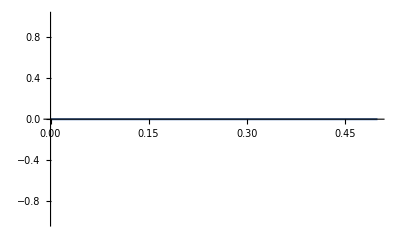

-Graphics3D-

-Graphics3D-

```mathematica
Remove[a]
Remove[b]
Remove[H]
a[t_] := a0 * (t/t0)^n;
b[r_] := b0*(r/r0)^3 + d0;

x = 3(a'[t]/a[t])^2 + b'[r]/(a[t]^2 * r^2);
H[t_] := (a'[t]/a[t]);
y = -(2*H'[t] + 3*H[t]^2) - b[r]/(a[t]^2 * r^3);
z = -(2*H'[t] + 3*H[t]^2) + (b[r]-r * b'[r])/(2 * a[t]^2 * r^3);
Simplify[x];
rho = ((8π + 5λ)*x + λ*y + 2*λ*z)/((8π + 4λ)*(8π + 2λ));
pr = (x+y - (8 + 2λ)*rho)/(8π + 2λ);
pt = (x +z - (8π + 2λ)*rho)/(8π + 2λ);
Simplify[rho];
Simplify[pr];
Simplify[pt];
b0 = 0;
d0 = r0;
λ = 0;
a0 = 1;
t0 = 1;
rho1 = (3 (t/t0)^(-2 n) (2 b0 t^2 (2 π+λ)+a0^2 n r0^3 (t/t0)^(2 n) (λ+n (4 π+λ))))/(4 a0^2 r0^3 t^2 (2 π+λ) (4 π+λ))
r0 = 100;
pr = ((t/t0)^(-2 n) (2 b0 r^3 t^2 (16 π^2+6 π (-4+λ)-λ (12+λ))-r0^3 (2 d0 t^2 (8 π^2+6 π λ+λ^2)+a0^2 n r^3 (t/t0)^(2 n) (-32 π^2-24 π λ-(-12+λ) λ+3 n (4+λ) (4 π+λ)))))/(4 a0^2 r^3 r0^3 t^2 (2 π+λ) (4 π+λ)^2)
pt =((t/t0)^(-2 n) (-2 b0 r^3 t^2 (2 π+λ)+r0^3 (d0 t^2 (2 π+λ)-a0^2 n r^3 (t/t0)^(2 n) (4 (-2+3 n) π+(-1+3 n) λ))))/(4 a0^2 r^3 r0^3 t^2 (2 π+λ) (4 π+λ))
Plot[rho1, {t,0,0.5}]
Plot3D[pr, {r,0,0.5},{t,0,0.5}]
Plot3D[pt, {r,0,0.5},{t,0,0.5}]
Quit[]
```